## Nucleation Analysis (Multi - stranded)

```mathematica
Needs["PlotLegends`"]
PartitionFunctionFILE="PartitionFunction_0_0.out";
FreeEnergyFileFILE="FreeEnergy_0_0.out";
PotentialDataFILE="POTENTIAL_DATA";
ParametersFILE="Parameters";

CollagenPATH="collagen/results/";

SetDirectory[FileNameJoin[{NotebookDirectory[]}]]

FrameBox["Numerical Parameters"]//DisplayForm
PartitionFunctionCollagen=Import[CollagenPATH<>PartitionFunctionFILE,"Table"];
FreeEnergyCollagen=Import[CollagenPATH<>FreeEnergyFileFILE,"Table"];
PotentialCollagen=Import[CollagenPATH<>PotentialDataFILE,"Table"];
ParametersCollagen=Import[CollagenPATH<>ParametersFILE,"Grid"]
Print["\n"]

L=IntegerPart[ParametersCollagen[[1,2]][[2]]];
m=IntegerPart[ParametersCollagen[[1,3]][[2]]];
n=IntegerPart[ParametersCollagen[[1,4]][[2]]];
kappa=IntegerPart[ParametersCollagen[[1,5]][[2]]];
sigma=IntegerPart[ParametersCollagen[[1,6]][[2]]];

Needs["PlotLegends`"]
```

/homes/ht/Desktop/collagen_nVa

Numerical Parameters

| 
L: | 5.
m: | 10
N: | 5
kappa: | 1.
sigma: | 1.
Delta: | 0.25
 | 
Extension Minimum: | 0
Extension Maximum: | 20

Results - Free Energy

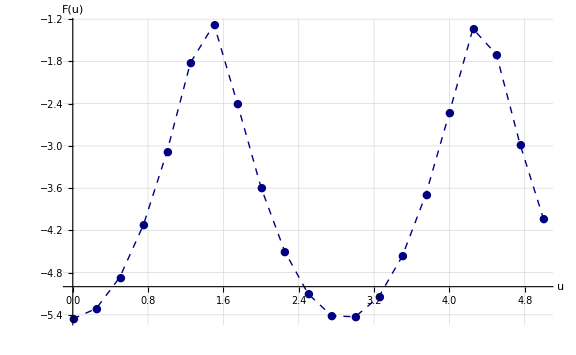

```mathematica
fsAxesLabel=24;
fs2=18;

plot=ListLinePlot[
{
FreeEnergyCollagen
},
PlotRange->All,
ImageSize->Large,
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesLabel->{
Style["u",FontSize->fsAxesLabel],
Style["F(u)",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
PlotStyle->{
{Thick,Dashed,Darker[Blue,0.5]}
},
PlotMarkers->{"●"},
PlotRange->All
]
```

```mathematica
Export["./col_numerical_N"<>ToString[n]<>"_L"<>ToString[L]<>"_m"<>ToString[m]<>"_kappa"<>ToString[kappa]<>"_sigma"<>ToString[sigma]<>".pdf",plot]
```

./col_numerical_N5_L5_m10_kappa1_sigma1.pdf